## The dynamical evolution of the EMS system in flat spacetime

#### the initial RN solution parameter setup finite‑difference matrix the KO dissipation matrix

{{0.565217,0.5,1},{2299.,4599.},{2001,0.000690345}}

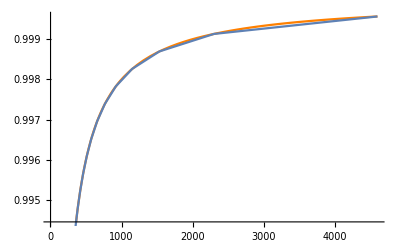

```mathematica
Off[Solve::ratnz,General::munfl]; 
{M=1.,Q=9/10,b0=-8,NN=2001};(*parameters  Grid size: 2^11+1*) 
amp=0.0001;
ζRNBH[r_]=(√((2M)/r-Q^2/r^2))/(√(1/r));RNBH[r_]=1-(√(1/r)ζRNBH[r])^2;(*the RN black hole,for comparison at the initial time*) 
sol=Sort[r/.Solve[RNBH[r]==0,r],#1>#2&];
{rh,rin}={M,1.3M};(*Inner boundary:slightly inside the horizon*) 
{zh,zin}=r/(M+r)/.{r->{rh,rin}};(*change of coordinates*) 
zout=1;(*Outer boundary:at infinity*) 
dz=(zout-zin)/(NN-1); 
z=Range[zin,zout,dz];(*a spatial grid with uniformly spaced points*)
zc=z;zc[[-1]]=zout(1-10^-15);(*avoid 1/0*)
{dz0,dz1}=NDSolve`FiniteDifferenceDerivative[Derivative[#],z,"DifferenceOrder"->4]["DifferentiationMatrix"]& /@ Range[0,1]; (*the fourth‑order accurate derivative matrix for the grid*)
kodissMatrix=NDSolve`FiniteDifferenceDerivative[Derivative[6],Range[Length[z]],"DifferenceOrder"->1]["DifferentiationMatrix"];(*KO dissipation*)
z2=Drop[z,-1];(*Separate treatment for outer boundary points*)
dt=6/10 Min[Differences[z2/(1-z2)]];
eps=1/128 dt/dz; (*the prefactor of the KO dissipation term*)

{{zin,zh,zout},{(z2/(1-z2))[[-2]],(z2/(1-z2))[[-1]]},{NN,dt}}

metricplot1=ListLinePlot[Thread[{r,RNBH[r]}/.r->z2/(1-z2)],PlotRange->All];
metricplot2=Plot[RNBH[r],{r,rin,z[[NN-1]]/(1-z[[NN-1]])},PlotStyle->Orange]; 
Show[metricplot2,metricplot1]
```

#### The initial conditions of the fields

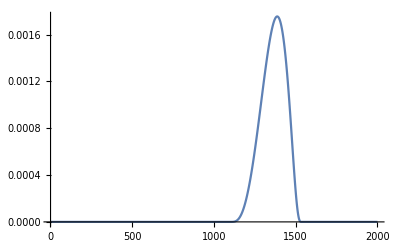

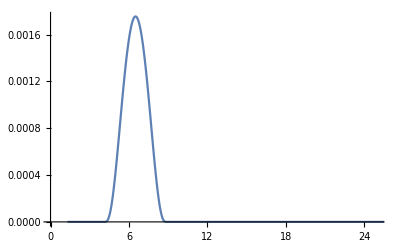

```mathematica
ic[r_,ru_,rl_]:=amp Piecewise[{{0, r≤rl}, {ⅇ^(-1/(ru-r)-1/(-rl+r)) (ru-r)^2 (-rl+r)^2, rl<r<ru}, {0, r>=ru}}]
ϕ0in=ic[#,9,4]&/@(z2/(1-z2));
ϕ0=Join[ϕ0in,{0}];(*Initial conditions*)
P0=(-1+z)^2 dz1.ϕ0;
Φ0=(-1+z)^2 dz1.ϕ0;
f[ϕ_]:=1/(1+b0 ϕ^2);(*the coupling function*) 
ListLinePlot[ϕ0,AxesOrigin->{rh,0},PlotRange->All]
ListLinePlot[Transpose[{z2/(1-z2),ϕ0in}],PlotRange->{{0,25},All}]
```

### The constraint equations and their solution

#### Outer‑boundary 𝜁 constraint equation (nonlinear; Newton–Raphson; used only initially)

```mathematica
(*Constraint equation for the metric α*)
```

```mathematica
ζdzIn=(-P (1/(1-x))^(7/2) x^(3/2) Φ-(Q^2/(x^2 ff[ϕ])+(x^2 (P^2+Φ^2))/(-1+x)^4)/(2 ζ[x])+ζ'[x]);(* ζConstraint equations (symbolic form),evaluated only at interior grid points*)

dζdzIn=D[ζdzIn/.ζ->Function[x,ζ[x]+ϵ dζ[x]],ϵ]/.ϵ->0;(*ζ Variational linear function;Jacobian matrix*)

dz0in=Most[dz0];dz1in=Most[dz1];(*Derivative matrices evaluated at interior grid points*)
(*PQx4/(-1+x)^4~~(x^2 (P^2+Φ^2))/(-1+x)^4*)
ζdzOut=(-(Q^2/ff[ϕ]+PQx4)/(2 ζ[x])+ζ'[x]); (*ζVariational linear function; Jacobian matrix; using L’Hôpital’s rule*)
dζdzOut=D[ζdzOut/.ζ->Function[x,ζ[x]+ϵ dζ[x]],ϵ]/.ϵ->0;
dz41=(dz1.dz1.dz1.dz1)[[-1]];
dz01=dz0[[-1]];
dz11=dz1[[-1]];
dz0first=dz0[[1]];
solveζ[ζ0t_,P0t_,Φ0t_,ϕ0t_]:=((*Newton–Raphson iteration for solving the constraint*)
ζ0temp=ζ0t;δζ=ζ0temp;
{P0tin,Φ0tin,ϕ0tin,fin}={Most[P0t],Most[Φ0t],Most[ϕ0t],Most[f[ϕ0t]]};(*Extract values at interior grid points*)
PQx4v=(dz41.(z^2 (P0t^2+Φ0t^2)))/24;(*L’Hôpital’s rule*)
ff1=f[ϕ0t[[-1]]];
While[Norm[δζ]>10^-12,
pairsIn={dζdzIn,-ζdzIn}/.{P->P0tin,Φ->Φ0tin,ϕ->ϕ0tin,ff[ϕ]->fin,x->z2,dζ[x]->dz0in,dζ'[x]->dz1in,ζ[x]->Most[ζ0temp], ζ'[x]->dz1in.ζ0temp};(*Jacobian matrix and equation values at interior grid points*)
pairsOut={dζdzOut,-ζdzOut}/.{PQx4->PQx4v,ff[ϕ]->ff1,ζ[x]->ζ0temp[[-1]], dζ[x]->dz01,dζ'[x]->dz11,ζ'[x]->dz11.ζ0temp};(*Jacobian matrix and equation values at the asymptotic boundary*)
pairsIn[[1,1]]=dz0first;
pairsIn[[2,1]]=0;
pairs={Join[pairsIn[[1]],{pairsOut[[1]]}],Join[pairsIn[[2]],{pairsOut[[2]]}]};(*Append the outer‑boundary contribution*)
δζ=LinearSolve@@pairs;(*Iteratively solve for the update at each step*)
ζ0temp=ζ0temp+δζ;
];
ζ0temp (*return the solution obtained*)
)
```

#### The α‑constraint equation and its solution (linear)

```mathematica
(*Constraint equation for the metric α*)
inv1z=Join[1/(1-z2),{0}];(*Boundary treated separately*) 
onelast=SparseArray[NN->1,NN];(*Boundary handling*)
lnadz=dz1;
lnadz[[-1]]=onelast;(*the boundary condition a[NN]=1*)
lnadzInv=Inverse[lnadz];
C0=inv1z^(7/2)z^(3/2);
solvea[ζ_,P_,Φ_]:=((*Linear equation used to solve for the metric α*)
Exp[-lnadzInv.((P Φ)/ζ C0)]
);
```

#### Solving α and φ in the spatial direction (required at every step)

```mathematica
C2=(-1+z)^2;
solveSpace[ζ_,P_,ϕ_]:=((*ζ fixed->solve α and Φ for later times*)
Φtemp0=C2 dz1.ϕ; 
{Φtemp0,solvea[ζ,P,Φtemp0]}
);
```

#### Metric initialization and initialization of all variables

```mathematica
solveSpace0[ζ_,P_,ϕ_]:=((*Treating ζ as a trial guess,solve for ζ to obtain the precise initial metric*)
Φtemp0=C2 dz1.ϕ;
ζtemp0=solveζ[ζ,P,Φtemp0,ϕ];
atemp0=solvea[ζtemp0,P,Φtemp0];
{Φtemp0,ζtemp0,atemp0}
);

ζ0=Join[ζRNBH[z2/(1-z2)],{√(2M)}];(*the initial trial value of ζ *) 
{Φt,ζt,at}=solveSpace0[ζ0,P0,ϕ0];(*Metric α and ζ at the initial time*)
{Pt,ϕt}={P0,ϕ0};(*Store the initial matter fields P,ϕ,Φ and the metric ζ,α*) 
(ζt[[-1]]-ζ0[[-1]])/ζ0[[-1]]
```

0.000113329

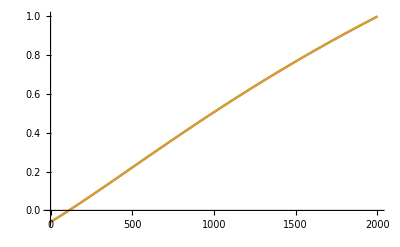

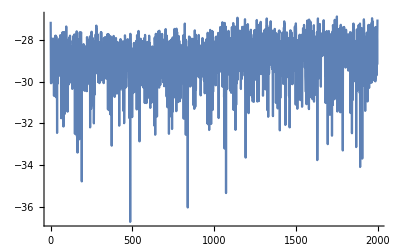

```mathematica
ListLinePlot[{Most[at^2(1-(√((1-z)/z)ζt)^2)],RNBH[z2/(1-z2)]},PlotRange->All]
ζdzConstraint[ζAll_,ζ_,P_,Φ_,ϕ_]:=((dz1in.ζAll)-Q^2/(2 z2^2 f[ϕ]ζ)-z2^(3/2)/(1-z2)^(7/2)P Φ-(z2^2 (P^2+Φ^2))/(2 (-1+z2)^4 ζ));(*the constraint equation for ζ*)
ListLinePlot[ζdzConstraint[ζt,Most[ζt],Most[Pt],Most[Φt],Most[ϕt]]//Rest//Abs//Log,PlotRange->All](*the
𝜁-constraint imposed at the initial time*)
```

### The evolution equations

```mathematica
C12=√((1-z)/z);
C1=z^2 inv1z^2;
C3=(2(1-z))/z;
C4=(Q^2 (-1+z)^4)/(2 z^4);
evolveTime[α_,ζ_,P_,Φ_,ϕ_]:=((*perform the evolution calculation for dζt,dPt and dϕt*)
{AA,BB}={α(P ζ C12 +Φ),α(P+C12 ζ Φ)};(*intermediate vars*)
{dζt,dPt,dϕt}={C1(AA BB)/(ζ α),C2 dz1.AA+ C3 AA+C4(α f'[ϕ])/f[ϕ]^2,BB}
);
```

### the RK4 time‑evolution loop

```mathematica
TStep=50;(*Save data every 100 steps*)
Offset[General::munfl]; 
t0=1;tn=t0;
```

```mathematica
T0=Floor[500/dt];(*Tt[0]=0;*)
Monitor[Timing[
While[tn<T0+1,(*the termination condition of the iteration*)
diss=eps*kodissMatrix.#&/@{ζt,Pt,ϕt};(*KO dissipation*)

(*RK4 step 1: Using values of a,ζ,P,Φ,ϕ at t, compute RK1 derivatives of ζ,P,ϕ at t*)
RK1=evolveTime[at,ζt,Pt,Φt,ϕt];

(*RK4 step 2: use RK1 to get ζ,P,ϕ at t+dt/2; update Φ,a; compute R2 derivatives of ζ,P,ϕ at t+dt/2*) 
{ζtemp,Ptemp,ϕtemp}={ζt,Pt,ϕt}+RK1*dt/2+1/2 diss;
{Φtemp,atemp}=solveSpace[ζtemp,Ptemp,ϕtemp]; 
RK2=evolveTime[atemp,ζtemp,Ptemp,Φtemp,ϕtemp];

(*RK4 step 3: use RK2 to get ζ,P,ϕ at t+dt/2; update Φ,a; compute R3 derivatives of ζ,P,ϕ at t+dt/2*)
{ζtemp,Ptemp,ϕtemp}={ζt,Pt,ϕt}+RK2*dt/2+1/2 diss;
{Φtemp,atemp}=solveSpace[ζtemp,Ptemp,ϕtemp]; 
RK3=evolveTime[atemp,ζtemp,Ptemp,Φtemp,ϕtemp];

(*RK4 step 4: use RK3 to get ζ,P,ϕ at t+dt; update Φ,a; compute RK4 derivatives of ζ,P,ϕ at t+dt*)
{ζtemp,Ptemp,ϕtemp}={ζt,Pt,ϕt}+RK3*dt+diss;
{Φtemp,atemp}=solveSpace[ζtemp,Ptemp,ϕtemp]; 
RK4=evolveTime[atemp,ζtemp,Ptemp,Φtemp,ϕtemp];

(*RK4 step 5:use RK1234 to compute ζ,P,ϕ derivatives at t+dt,then update Φ and 𝑎*)
{ζtemp,Ptemp,ϕtemp}={ζt,Pt,ϕt}+(RK1+2RK2+2RK3+RK4)*dt/6+diss;
{Φtemp,atemp}=solveSpace[ζtemp,Ptemp,ϕtemp]; 
{Ptemp[[-1]]=0;Φtemp[[-1]]=0;ϕtemp[[-1]]=0};(*Boundary conditions for matter fields*)
{at,ζt,Pt,Φt,ϕt}={atemp,ζtemp,Ptemp,Φtemp,ϕtemp};(*save all variables at t+dt for the next step*)

(*End of each iteration:save data every TStep steps*) 
If[Mod[tn,TStep]==1,
{att[tn],ζtt[tn],Ptt[tn],Φtt[tn],ϕtt[tn],ρtt[tn]}={at,ζt,Pt,Φt,ϕt,
1/2*(Pt^2+Φt^2)+(Q^2*(1+b0*ϕt^2))/2*(1-z)^4/z^4};
ζcst[tn]=ζdzConstraint[ζt,Most[ζt],Most[Pt],Most[Φt],Most[ϕt]](*save constraints every TStep steps*)
];
tn=tn+1;(*record iteration numbers*)
]],{tn,tn*dt,ϕt[[1]]}]//AbsoluteTiming
```

{6721.73,{6667.7,Null}}

```mathematica
{dt tn,tn}
```

{500.,724276}

## Analysis of numerical results

```mathematica
tns=Range[1,Floor[tn/TStep-1]TStep+1,TStep];(*The iteration steps associated with all saved data*)
times=dt tns;(*The coordinate-time values associated with all saved data*)
```

#### The 𝜁 constraint violation

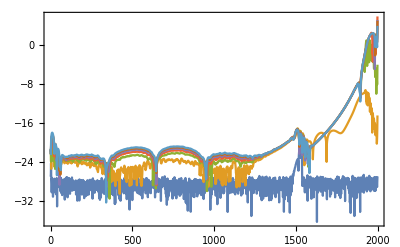

```mathematica
(*The final‑time 𝜁 constraint violation*) 
ListLinePlot[Rest[ζcst[tns[[-1]]]]//Abs//Log,PlotRange->All];
ListLinePlot[(Rest[ζcst[#]]//Abs//Log)&/@tns[[1;;-1;;Floor[Length[tns]/6]]],Frame->True,PlotRange->All]
```

### Metric and scalar‑field profiles

#### Metric profile

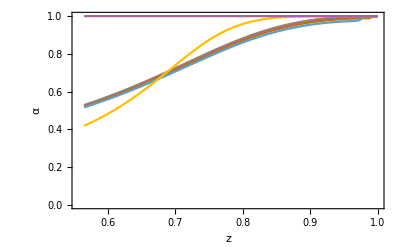

```mathematica
ListLinePlot[Transpose[{z,att[#]}]&/@tns[[-1;;1;;-Floor[Length[tns]/8]]],Frame->True,LabelStyle->{16,FontFamily->Times},FrameLabel->{"z","α"}](*Snapshots of the evolution of the metric function
𝛼*)
```

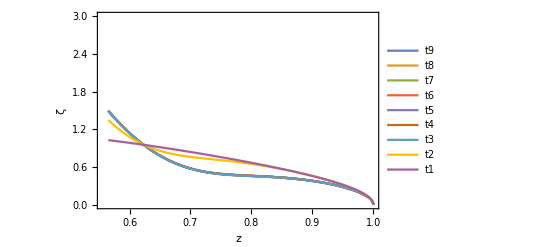

```mathematica
ζz[t_]:=√((1-z)/z)ζtt[t];(*Metric ζ/(√r)*)
gttz[t_]:=att[t]^2(1-ζz[t]^2);(*Metric coefficient of dt^2*) 
gttr[tn0_]:=Transpose[{z2/(1-z2),Most[gttz[tn0]]}];(*Metric coefficient of dt^2*) 
ListLinePlot[Transpose[{z,ζz[#]}]&/@tns[[-1;;1;;-Floor[Length[tns]/8]]],Frame->True,LabelStyle->{15,FontFamily->Times},FrameLabel->{"z","ζ"},PlotRange->{All,{0,3}},PlotLegends->{"t9","t8","t7","t6","t5","t4","t3","t2","t1"}](*Snapshots of the evolution of the metric function
𝜁*)
```

#### The location of the outer horizon

```mathematica
metricαrF[t_]:=Interpolation[gttr[t]];
irrBHrn=(x/.FindRoot[metricαrF[#][x]==0,{x,1.4rh}])&/@tns;
```

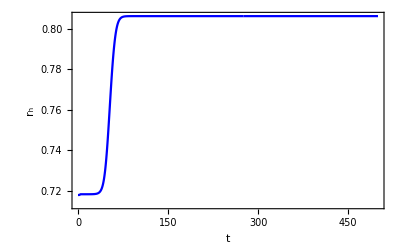

```mathematica
irrBHtrn=Transpose[{times,1/2 irrBHrn}]; 
irrBHtrf=Interpolation[irrBHtrn];
ListLinePlot[irrBHtrn,PlotRange->All,PlotStyle->Blue,Frame->True,LabelStyle->{15,FontFamily->Times},FrameLabel->{"t","r_h"}]
Plot[Log[irrBHtrf'[t]],{t,times[[1]],times[[-1]]}];
```

### The scalar field at the outer horizon

#### Scalar-field value at the horizon

```mathematica
ϕtr[t_]:=Transpose[{z2/(1-z2),ϕtt[t]//Most}];
ϕtz[t_]:=Transpose[{z2,ϕtt[t]//Most}];
ϕtrF[t_]:=Interpolation[ϕtr[t]];
ϕRH=ϕtrF[tns[[#]]][irrBHrn[[#]]]&/@Range[Length[tns]];
```

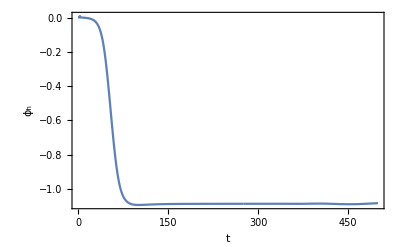

```mathematica
ϕRHtrn=Transpose[{times,ϕRH}]; 
ϕRHtrf=Interpolation[ϕRHtrn];
ListLinePlot[ϕRHtrn,PlotRange->All,Frame->True,LabelStyle->{15,FontFamily->Times},FrameLabel->{"t","ϕ_h"}](*Scalar-field value at the horizon*)
```

#### Scalar curvature

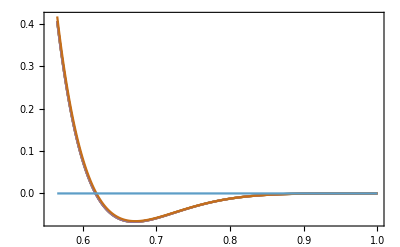

```mathematica
Rtz[t_]:=Ptt[t]^2-Φtt[t]^2;(*Metric coefficient of dt^2*) 
Rtr[tn0_]:=Transpose[{z2/(1-z2),Most[Rtz[tn0]]}];(*Metric coefficient of dt^2*) 
ListLinePlot[Transpose[{z,Rtz[#]}]&/@tns[[-1;;1;;-Floor[Length[tns]/6]]],Frame->True,PlotRange->All]
```

```mathematica
RtrF[t_]:=Interpolation[Rtr[t]];
RRH=RtrF[tns[[#]]][irrBHrn[[#]]]&/@Range[Length[tns]];
```

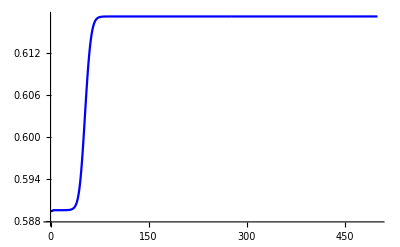

```mathematica
ListLinePlot[Transpose[{times,irrBHrn/(1+irrBHrn)}],PlotRange->All,PlotStyle->Blue]
ListPlot[Transpose[{times,RRH}]];
```

#### Scalar-field profile

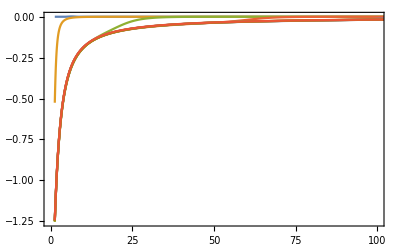

```mathematica
ListLinePlot[ϕtr[#]&/@tns[[1;;-1;;Floor[Length[tns]/10]]],Frame->True,AxesOrigin->{rh,0},PlotRange->{{0,100},All}]
(*Snapshots of the evolution of the scalar field as a function of r*)
```

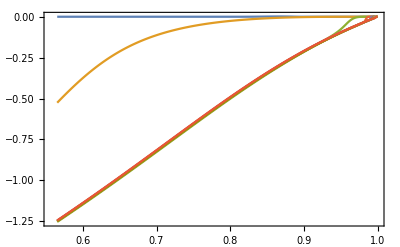

```mathematica
ListLinePlot[ϕtz[#]&/@tns[[1;;-1;;Floor[Length[tns]/10]]],Frame->True,PlotRange->All] (*Snapshots of the evolution of the scalar field as a function of z*)
```

### Mass distribution and the horizon

#### Misner-Sharp mass

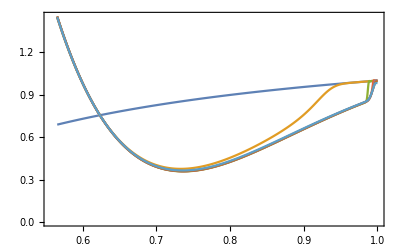

```mathematica
misnerSharpz[t_]:=ζtt[t]^2/2;(*Misner-Sharp mass*)
misnerSharpr[t_]:=Transpose[{z2/(1-z2),misnerSharpz[t]//Most}];(*Misner-Sharp mass*)
ListLinePlot[Transpose[{z,misnerSharpz[#]}]&/@tns[[1;;-1;;Floor[Length[tns]/6]]],Frame->True,PlotRange->All](*Snapshots of the evolution of the Misner–Sharp mass*)
```

### Kretschmann scalar and Energy density

#### Kretschmann scalar

```mathematica
rr=Join[z2/(1-z2),{10^8}];
RuuuuRdddd[t_]:=8 (Ptt[t]^2-Φtt[t]^2)^2-(8 ζz[t]^2)/rr^2(Ptt[t]^2-Φtt[t]^2)+(12 ζz[t]^4)/rr^4+(20 Q^4)/(rr^8 f[ϕtt[t]]^2)+(16 Q^2 (Ptt[t]^2-Φtt[t]^2))/(rr^4 f[ϕtt[t]])-(24 Q^2 ζz[t]^2)/(rr^6 f[ϕtt[t]])(*The formula for the Kretschmann scalar*)
```

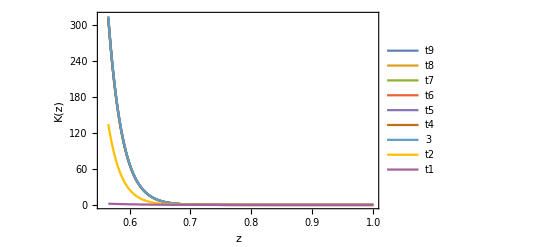

```mathematica
ListLinePlot[Transpose[{z,RuuuuRdddd[#]}]&/@tns[[-1;;1;;-Floor[Length[tns]/8]]],PlotRange->All,Frame->True,FrameLabel->{"z","K(z)"},LabelStyle->{15,FontFamily->Times},PlotLegends->{"t9","t8","t7","t6","t5","t4","3","t2","t1"}](*Snapshots of the evolution of the Kretschmann scalar*)
```

```mathematica
RRtn=RuuuuRdddd[#][[1]]&/@tns;
```

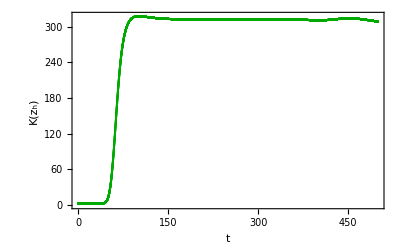

```mathematica
ListPlot[Transpose[{times,RRtn}],Frame->True,FrameLabel->{"t","K(z_h)"},PlotRange->All,LabelStyle->{15,FontFamily->Times},PlotStyle->Darker[Green]](*Time evolution of the Kretschmann scalar inside the outer horizon*)
```

#### Energy density

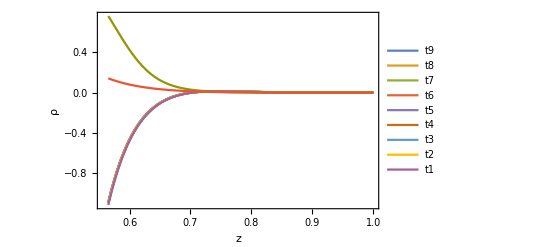

```mathematica
ListLinePlot[Transpose[{z,ρtt[#]}]&/@tns[[-1;;1;;-Floor[Length[tns]/10]]],Frame->True,LabelStyle->{15,FontFamily->Times},FrameLabel->{"z","ρ"},PlotLegends->{"t9","t8","t7","t6","t5","t4","t3","t2","t1"},PlotRange->All](*Snapshots of the evolution of the energy density*)
```

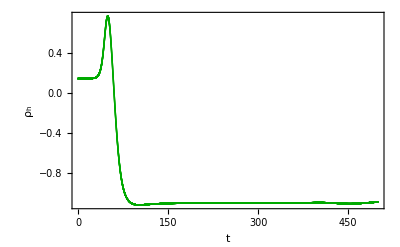

```mathematica
ρttn=ρtt[#][[1]]&/@tns;
ListPlot[Transpose[{times,ρttn}],Frame->True,LabelStyle->{15,FontFamily->Times},FrameLabel->{"t","ρ_h"},PlotStyle->Darker[Green],PlotRange->All](*Time evolution of the energy density inside the outer horizon*)
```